```mathematica
(*Run this cell to delete all notebook output and delete all blank input cells. Makes some of the numerics cells behave weird the next time you evaluate them, but if you evaluate the numerics cells again a second time then it works out. *)
NotebookDelete[Cells[EvaluationNotebook[],GeneratedCell->True]]
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&];
```

# Bloch Oscillations

## Introduction

The goal of this notebook is, in Norm’s words, to teach you “Everything you ever wanted to know about Bloch oscillations”. This is based off of a number of sources. I started from basic AMO concepts outlined in “Bloch oscillations of cold atoms in optical lattices”, a 2004 paper by Kolovsky and Korsch. From there, I matched these results up with Chenghui’s 2018 thesis, a paper “Theoretical analysis of a large momentum beamsplitter using Bloch oscillations” by Biraben’s group from 2010 (which was mostly correct, but I found one typo in their definition of U_0 which they later corrected in their α paper), Matt Jaffe’s code in Mathematica/Matlab and documentation in One Note, and Richard Parker’s code in Matlab.

The basic Hamiltonian of an atom in an optical lattice (OL) is given by:

H_OL = (p̂)^2/(2M)+V_0(cos(kx))^2 = (p̂)^2/(2M)+V_0/2(1+cos(2kx))  = (p̂)^2/(2M)+ℏΩ_eff cos(2kx) + ℏω_Stark
 
 You’ll see people write this in different ways, but the main idea is that the laser field causes an AC Stark shift of the atom, changing the atom’s energy as a function of position. The energy shift comes from the electric field of light polarizing the atom, which causes its energy to shift. For AC electric fields near an atomic resonance, this energy shift is given by:
 
 ℏΩ_eff= ℏΩ^2/(2Δ)= V_0/2
 
We typically call V_0 the lattice depth, since it is the depth of the AC Stark shift potential. The AC Stark shift depends on the electric field squared, so it has half the wavelength of the laser light. This can be seen explicitly in the cos(2kx) term in the optical lattice potential. For blue detuned light, ℏΩ_eff>0 so atoms get pushed away from regions of high intensity and trapped near the nodes. For red detuned light, ℏΩ_eff<0 so atoms are attracted to regions of high intensity.

## Bloch Oscillations in Lattice Frame

Bloch Oscillations occur when a particle is in a periodic potential and experiences a constant force. The particle accelerates, but when it reaches the first Bragg resonance (the edge of the first Brillion zone) it reflects off of the lattice. The particle will continue to bounce off the lattice and “oscillate” in place, recieving momentum kicks once per Bloch period. 

	The easiest way to study the problem is to work in the frame of the lattice, so that in this frame the lattice is stationary. Our Hamiltonian in the lattice frame becomes:

H_lattice = (p̂)^2/(2M)+ℏΩ_eff(1+cos(2kx) ) -Fx

This Hamiltonian is the standard AC Stark shift potential but with an added force term Fx, written with the convention that a positive force F > 0 will accelerate you in the +x direction. In the optical cavity experiment lattice hold geometry, the lattice frame is equivalent to the lab frame, since the lattice is at rest in the lab and gravity creates a force on the atoms. In the atomic fountain experiment, we realize this Hamiltonian not by adding a force to the atoms, but by accelerating the lattice. We ramp laser frequencies to “subtract off” gravity, so you never need to think about gravity for the fountain’s Bloch oscillations. In the frame of the lattice (an accelerating/non-inertial frame) it looks like the atom is accelerating backwards, so we use a “fictitious” force.

	A long time ago, Houston worked out the eigenstates of this Hamiltonian, and these basis states are called Houston functions. The main realization is that a uniform force will add momentum linearly in time, since dp/dt = F. When there is an optical lattice, we talk about quasimomentum instead of momentum, so Houston worked out that the quasimomentum of the atom is ramped linearly in time. You can write any general state as a sum over Houston functions:

Φ(t)=   ∑_n c_n(t) e^(-i/ℏ∫dτ E_(n, κ_q(τ)))e^(i κ_q(t) x)u_(n, κ_q(t))(x)

The index n labels the energy level of the state (I’ll use n=1 is the ground state because counting should begin with 1....).  κ_q(t)  is the quasimomentum of the state (defined modulo 2 k, ie. only withing a Brillion zone), and it is assumed that the quasimomentum increases linearly in time when a constant force is applied: κ_q(t) = κ_0- Ft/ℏ, and  κ_0  is the initial momentum of the atom when it is first loaded into the lattice.. “Quasimomentum” is a fancy word for momentum of particles inside of a periodic potential. One way to think about it is that if you adiabatically turn off the lattice potential, the quasimomentum becomes the actual momentum of the particle. The factor  u_(n, κ_q(t))(x)  is a periodic spatial function with the same periodicity of the lattice (periodicity of λ/2), commonly called a “Bloch wave”.  The  e^(-i/ℏ∫dτ E_(n, κ_q(τ))) term is just a phase term accounting for the standard phase evolution of an eigenstate, ϕ(t) = -i/ℏ(∫_0)^t dt' E(t') .

	If you plug the Houston function into the Schrodinger equation, you’ll see that everything cancels nicely, in particular, the derivatives of the  e^(i κ_q(t) x) term bring down a force term that cancels the -Fx term in the Hamiltonian, and then the u_(n, κ_q(t))(x) is already an eigenstate of an optical lattice.

	When you have a spatially periodic potential, it is often much easier to simulate dynamics in momentum space instead of real space, so we solve for the wavefunction ψ(k,t) instead of ψ(x,t). There are a number of ways of seeing why this is true, perhaps the easiest is that the Houston wave functions have the same periodicity as the lattice, so we can expand the spatially periodic part of the wavefunction (the “Bloch wave”) into Fourier components. Since the potential is written as cos(2kx) = 1/2 (e^ⅈ2kx+e^-ⅈ2kx), when you plug a Fourier wave into the Schrodinger equation you’ll see that these +/- exponential terms couple each momentum state k’ to its nearest neighbors k’+2k and k’-2k. So each momentum state is only coupled to two other states, making simulation easy (as opposed to coupling between all states).
	
	For simulation we also allow the phase evolution of the eigenstate to be implicitly captured by the simulation instead of needing to solve for it exactly. So we use the ansatz:
	
	ψ(t) = (Σ_(-∞))^∞ c_m(t) e^(i (κ(t) + 2 m k) x)
	
Where we sum over the Fourier coefficients indexed by integer m. Writing the state this way assumes it is spatially periodic with period λ/2, ie. it is a plane wave. This is equivalent to assuming that we have infinitely cold atoms, since they have no spread in momentum. If you want to take into account finite temperature effects, you need to turn this sum into an integral, and then the calculations get a lot harder because you need to solve for many more state coefficients. 

We now want to solve for c_m(t), since this will tell us everything about the state as a function of time. If you plug this state into the Schrodinger equation, you get the following equations of motion:	
	
	i ℏ (ċ)_m = (((ℏ^2(κ(t)+2m k))^2)/(2M) + ℏΩ_eff)c_m+ ℏΩ_eff/2(e^(-2i k x)+e^(+2 i k x))c_m= (((ℏ^2(κ(t)+2m k))^2)/(2M) + ℏΩ_eff)c_m+ ℏΩ_eff/2(c_(m-1)+c_(m+1))  

The p^2/(2m) kinetic energy operator just pulls down the momentum in the exponential terms, and the potential couples the c_m state to its nearest neighbors.

The right hand side of this equation is the Hamiltonian operator acting on the state. If we write the Hamiltonian operator in matrix form, we can solve for the energy eigenstates, or band structure, in code. I will plot two things: 1) the energy band structure as a function of initial momentum of the atom κ_0, and 2) the energy band structure over time for an atom that started with κ_0=0. Also, I set ℏω_Stark = 0, since this is a DC energy shift that is equal for all energy levels so it doesn’t affect the dynamics that we’re interested in. I used dimensionless units for everything (ℏ = k = m = 1), more on this below.

Matrix form of the Hamiltonian:

((-8+k0-F t)^2 | Ω/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/4 | (-6+k0-F t)^2 | Ω/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | Ω/4 | (-4+k0-F t)^2 | Ω/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ω/4 | (-2+k0-F t)^2 | Ω/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | Ω/4 | (k0-F t)^2 | Ω/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | Ω/4 | (2+k0-F t)^2 | Ω/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | Ω/4 | (4+k0-F t)^2 | Ω/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | Ω/4 | (6+k0-F t)^2 | Ω/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/4 | (8+k0-F t)^2)

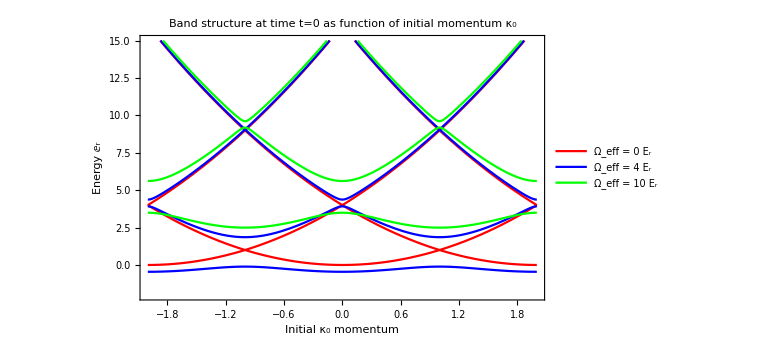

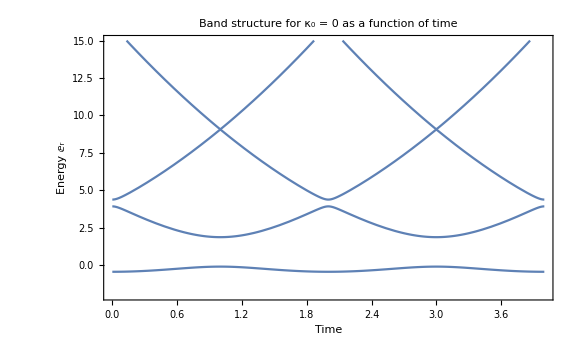

```mathematica
ClearAll["Global`*"];
kMax = 4;  (*maximum momentum state cutoff*)
dim = 2 kMax+1;   (*dimension of Hamiltonian matrix*)
Ham[k0_, F_, t_, Ω_] = Normal[SparseArray[{{m_,m_}:>(k0-F t + 2(m - (kMax+1)))^2 ,{i_,j_}:>Ω/4/;Abs[i-j]==1},{dim,dim}]];

Print["Matrix form of the Hamiltonian:"]
MatrixForm[Ham[k0, F, t, Ω]]

BlochBands[k0_,F_,t_,Ω_] :=Eigensystem[Ham[k0, F, t, Ω]]⟦1⟧;

BS1 = Plot[{BlochBands[k0, 0, 0, 0], BlochBands[k0, 0, 0, 4], BlochBands[k0, 0, 0, 10]}, {k0, -2, 2}, PlotStyle->{Red, Blue, Green}, PlotRange->{-2, 15}, Frame->True,FrameLabel->{Initial momentum Subscript[κ, 0],Energy (Subscript[E, r])} , PlotLegends->{"Ω_eff = 0 E_r", "Ω_eff = 4 E_r", "Ω_eff = 10 E_r"}, PlotLabel->"Band structure at time t=0 as function of initial momentum κ_0", ImageSize-> Large]

BS2 = Plot[BlochBands[0, 1, t, 4], {t, 0, 4}, PlotRange->{-2, 15}, Frame->True,FrameLabel->{Time,Energy (Subscript[E, r])} , PlotLabel->"Band structure for κ_0 = 0 as a function of time", ImageSize-> Large]
```

## Bloch Oscillations in Inertial Frame

Now, let’s consider Bloch oscillations from a different frame of reference, namely an inertial frame of the atom. I mentioned before that we don’t actually apply a force to atoms, we just accelerate the optical lattice. So in the atom’s inertial frame, it looks like the lattice is accelerating away with some acceleration a:

H_inertial =(p̂)^2/(2M)+V_0 cos^2(k(x - 1/2 a t^2))  

Experimentally, in the fountain we accomplish this by ramping the frequency difference between the counter-propagating laser beams that form the optical lattice. When two conter-propagating lasers have a frequency difference (typically ~ 10 x 2π kHz), the optical lattice moves at some velocity (typically on the order of tens of mm/s), and linearly ramping this frequency difference accelerates the lattice. We care about the sum of the electric fields squared: you can expand the (cos(kx-ωt) + cos(k x+ω't))^2 term in the potential, and after making a rotating wave approximation, the remaining term is cos(2k x-Δωt) , ie. we get a lattice moves at a velocity of v = Δω/(2k) (where Δω = ω - ω’). This implies that if we ramp the frequency difference at a rate r, we get the following relationships:  

r=(d(Δω))/dt = 2k dv/dt= 2k a = (2k F)/M_cs,    or    F = (r M_Cs)/(2k)

All of the simulations below are written in terms of the ramp rate r because this is the experimentally relevant parameter, it’s what we program into the DDS. Writing the inertial Hamiltonian in terms of the optical frequency differences, we have:

H_inertial = (p̂)^2/(2M)+ℏΩ_eff cos(2 k x - Δϕ(t))               where                  Δϕ(t) = (∫_0)^t dτ Δω(τ)

For constant frequency ramp rates r, we get 

Δϕ(t) = (∫_0)^t dτ Δω(τ)  = (∫_0)^t dτ (ω_0 + r t) = Δω_0 t + (r t^2)/2 = 2 k v_0 t + (r t^2)/2

For references about this integral, see the appendix of “Bloch oscillations of atoms, adiabatic rapid passage, and monokinetic atomic beams” as well as Tim Kovachy’s paper “Optical Lattices as Waveguides and Beam Splitters for Atom Interferometry: An Analytical Treatment and Proposal of Applications” (It took me a long time to find a factor of 2 error in Richard’s Bloch oscillation code, it ended up coming from this integral). 

Plugging this into the Hamiltonian, we have

H_inertial = (p̂)^2/(2M)+ℏΩ_eff/2(e^(2 i k x + i (Δω_0 t + (r t^2)/2)) + e^(-2 i k x - i(Δω_0 t + (r t^2)/2)) + 2)

and we get the following equations of motion:

 i ℏ(ċ)_m(t) = ((κ(t)+2m)^2/(2 M_Cs) + ℏΩ_eff/2)c_m+ ℏΩ_eff/4( e^(i(Δω_0 + (r t^2)/2))c_(m-1)+ e^(-i(Δω_0 + (r t^2)/2))c_(m+1))

### Note on unitary transformations

In quantum mechanics, you can boost between different frames of reference using Unitary transformations. For example, you can perform translations in space and in momentum space, and you can boost into accelerating frames. It is possible to perform a unitary transformation to tranform between  H_lattice  and  H_inertial. You can see

## Dimensionless Units

If you've never used dimensionless units before, the idea is that you choose a "natural" set of units for the problem so that most numbers are near 1. It helps prevent, for example, numerical errors from having ℏ ~ 10^-34 floating around in the same equations as frequencies ω ~ 10^4. It is THE way to do numerics, and then one can convert back to real units after simulations are done.  We set ℏ = M = 1. The only thing we need to decide on is which length scale to set equal to 1: we choose k = 1. Some useful relationships regarding this choice of dimensionless units in Bloch oscillations:

The recoil energy E_r is defined as E_r = (ℏ^2 k^2)/(2m) = 1/2. Since E_r = ℏ ω_r, we have ω_r = 1/2

Time/ frequency ramp:     t → ω_r^-1 τ  =  2 τ,         r→ ω_r^2 r'  =  r'/4 

Distance:   since k = 1,        λ = (2π)/k = 2π,  so each lattice site is spaced by λ/2 = π

Velocity:  The recoil velocity v_r is       v_r = (ℏ k)/m = 1

The Bloch period:   T_b = (4π ℏ)/(F d)=4 ℏk^2/(r M),           or in dimensionless form,           ω_r^-1 τ_bloch = 4/(ω_r^2 r')      →   τ_bloch = 8/r'  

Energy relationships:               Ω_eff= Ω^2/(2δ)= Γ^2/(4δ) I/I_sat =V_0/(2ℏ) ,         it is useful in simulation to define V’ such that V_0=V' E_r = V'/2 , and V’ is the dimensionless lattice depth.

Quasimomentum:   κ(t)→ k(κ_0' - (r t)/2)   =   k(κ_0' - ((ω_r^2 r')(ω_r^-1 τ))/2  )    
which means that the dimensionless quasimomentum ramps as     κ'(τ)→ κ_0' - (r' τ)/4 

From these relationships, we can derive the dimensionless equations of motion for simulation:

Lattice frame equations of motion:   

    ⅈ/2 (ċ)_m(τ) = ((κ(t)+2m)^2/2 + V'/4)c_m+ V'/8(c_(m-1)+c_(m+1))                   
  →                  ⅈ (ċ)_m(τ) = ((κ'(t)+2m)^2 + V'/2)c_m+ V'/4(c_(m-1)+c_(m+1))   
    
The bold equation is the equations of motion I use for lattice frame simulations. 

Inertial frame equations of motion:

ⅈ/2 (ċ)_m(τ) = ((κ(τ)+2m)^2/2 + V'/4)c_m+ V'/8( e^(i(Δω'_0 τ + (r t^2)/2))c_(m-1)+ e^(-i(Δω'_0 τ+ (r t^2)/2))c_(m+1)) 
	→          ⅈ (ċ)_m(τ) = ((κ(τ)+2m)^2 + V'/2)c_m+ V'/4( e^(i(Δω'_0 τ + (r' t^2)/2))c_(m-1)+ e^(-i(Δω'_0 τ + (r' τ^2)/2))c_(m+1)) 

For reference, I put here the inertial frame Hamiltonian in matrix form, where I drop the constant AC Stark shift offset:

```mathematica
ClearAll["Global`*"];
kMax = 4;
dim = 2 kMax+1;
Ham[k0_, r_,t_,V_] = Normal[SparseArray[{{m_,m_}:>(k0 + 2(m - (kMax+1)))^2,{i_,j_}:>V/4 Exp[ⅈ/2 r t^2]/;i-j==1,{i_,j_}:>V/4 Exp[-ⅈ/2 r t^2]/;j-i==1},{dim,dim}]];
Print["Matrix form of the inertial frame Hamiltonian:"]
MatrixForm[Ham[k0, r,t,V]]
```

Matrix form of the inertial frame Hamiltonian:

((-8+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 ⅇ^(1/2 ⅈ r t^2) V | (-6+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (-4+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (-2+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | k0^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (2+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (4+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (6+k0)^2 | 1/4 ⅇ^(-1/2 ⅈ r t^2) V
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 ⅇ^(1/2 ⅈ r t^2) V | (8+k0)^2)

## Numerical simulation of Bloch oscillations

Now that we’ve worked out the dimensionless equations of motion, we can numerically integrate these differential equations to solve for the evolution of an atomic state given actual experimental parameters. Below, you can toggle back and forth between the two different Hamiltonians (lattice frame and inertial frame) by commenting one or the other out. The code sets up a system of coupled equations for all of the coefficients c_m. We cut off momentum states at some values +/- kMax since they don’t contribute to the dynamics.

Hamiltonian matrix for Bloch oscillations:

((-17.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/2 | (-15.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | (-13.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/2 | (-11.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3/2 | (-9.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3/2 | (-7.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/2 | (-5.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (-3.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (-1.9-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (0.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (2.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (4.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (6.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (8.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (10.1-0.2144 t)^2 | 3/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (12.1-0.2144 t)^2 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (14.1-0.2144 t)^2 | 3/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (16.1-0.2144 t)^2 | 3/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2 | (18.1-0.2144 t)^2)

Wavefunction after loading lattice:

{5.9213×10^-31,2.45857×10^-26,7.86421×10^-22,1.54486×10^-17,1.5576×10^-13,7.08462×10^-10,1.27505×10^-6,0.000735518,0.0875734,0.832493,0.0785973,0.000596274,9.50067×10^-7,4.90927×10^-10,1.08309×10^-13,1.20363×10^-17,1.26329×10^-21,6.44483×10^-19,1.34933×10^-15}

Projection onto first three Bloch bands after loading lattice:

Ground state: 0.999353, First excited state: 0.000550422, Second excited state: 0.0000943775

Wavefunction after Bloch oscillations:

{6.82223×10^-8,6.17649×10^-11,7.63599×10^-15,7.63064×10^-16,2.11974×10^-14,4.89082×10^-15,4.00304×10^-11,1.6291×10^-7,0.0000999961,0.000181038,0.000119838,0.0000620788,0.0000517145,0.00114166,0.0993935,0.831044,0.0674216,0.000481279,7.42386×10^-7}

Projection onto first three Bloch bands after Bloch oscillations:

Ground state: 0.999163, First excited state: 0.000302764, Second excited state: 2.54419×10^-6

Wavefunction after unloading lattice:

{2.14604×10^-8,1.4911×10^-11,2.71826×10^-19,5.87172×10^-16,2.09337×10^-14,7.34064×10^-16,4.59564×10^-12,6.08975×10^-8,0.0000986691,0.000181448,0.000113762,0.0000637872,0.0000430239,0.0000278174,0.00133723,0.997959,0.000172636,3.13209×10^-8,4.47262×10^-13}

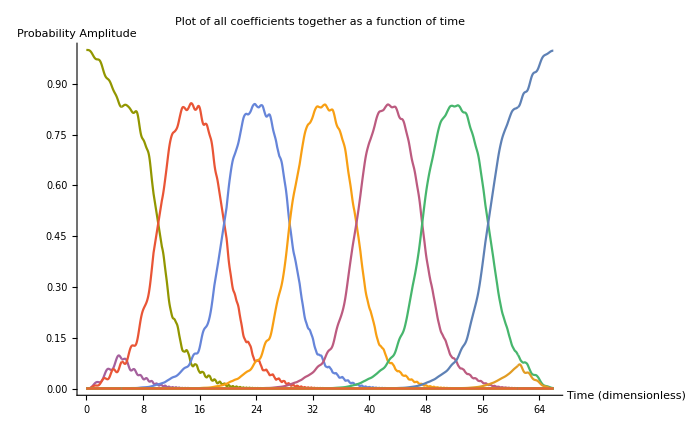

```mathematica
ClearAll["Global`*"];

rGrav = 0.8576; (*This is the dimensionless ramp rate for 852nm light that corresponds to gravitational acceleration 9.8 m/s^2. This value is 23 kHz/ms converted with a factor of 2 π x (2.066 kHz)^2. We need to convert both 1/s units, but the 23 KHz number is in Hz, not radians/s, so we only need one factor of 2π. *)

(*User defined constants*)

NLatDep = 6;  (*Dimensionless lattice depth, called V' in above text*)
NBloch = 6;    (*Number of Bloch oscillations to simulate*)
r = rGrav;  (*r is the dimensionless ramp rate. For gravity, set r = rGrav*)
v0 = 0.1;    (*Dimensionless initial velocity, in units of recoil velocity Subscript[v, r]. v0 = 1 corresponds to edge of first Brillion zone. Also, if you make v0 close to the edge of a Brillion zone boundary (near 1, 3, 5, etc.) then you need to make tLoad much larger in order to adiabatically load into the ground state. This is because the energy gap between levels is much smaller here. The code should work for any value of v0 that you put in (if you try v0>20 it will get very slow to simulate because you will blow up the size of the Hamiltonian matrix) *)
tLoad = 5;  (*Length of time used to adiabatically load state into the lattice *)
debug = 1;   (* Set to 1 for extra imformation throughout the simulation, or 0 if you get irritated with all the info *)

(*Implicitly defined constants*)

k0 = Mod[v0+1,2]-1 ;  (*Initial quasimomentum, defined in the range [-1,1) *)
n0 = IntegerPart[(v0 - k0)/2];                       (* Initial momentum state based on v0*)
Δw = 8 n0;                            (* This is the initial frequency required to load the inital atom into the ground state of the lattice. If you change v0 enough such that you are in a different Brillion zone, the code shifts the initial velocity of the lattice so that you still catch the atom in the ground state. *)
κ = NLatDep/8;
BlochPeriod = 8/r;
TBloch = BlochPeriod * NBloch;
kMax = Max[5,NBloch + 3 + n0];  (*This ensures that in the worst case scenario, amplitude never hits the momentum boundaries of the simulation. VERY deep lattice depths will require extra momentum states as padding since these states may actually get populated*)
dim = kMax*2+1;

(*This loadLattice module creates the initial state and loads it into the lattice. It takes in an initial free space momentum state n0 for a wavefunction, size of the hamiltonian being simulated, time to load lattice, and a load hamiltonian which is a function of time. It solves the Schrodinger equation for 
the wave function while loading the atom into the lattice  and returns this wave function. *)

loadLattice[kMax_, nn0_, tLoad_, loadHam_]:= Module[{maxK= kMax, n0 = nn0, loadTime = tLoad, HamLoad = loadHam},
Clear[ψ, ψi, ψci, ics, cs];

dimState = 2*maxK + 1;
ψi = ConstantArray[0,dimState];
ψi⟦n0 + maxK+1⟧ = 1;

ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];
ics = Table[ ci[n][0]==ψi⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ HamLoad[t].ψ[t];
sol = NDSolve[{equation,ics},cs,{t,0,loadTime}];
ψcii[t_]=ψ[t]/.sol⟦1⟧;
ψcii      (*Returns full wavefunction, including time dependence*)
]

(*unloadLattice is a module that takes in the size of the hamiltonian being simulated, the time taken to unload the atoms (assumed to be the same as the load time), the unload hamiltonian as a function of time, and the state to be unloaded. It returns the state evolution during unload, so ψci[tLoad] is the final free space wavefunction. *)

unLoadLattice[kMax_, tLoad_, unLoadHam_, ψci_]:= Module[{maxK= kMax, loadTime = tLoad, HamUnLoad = unLoadHam, ψi= ψci},
Clear[ψ, ics, cs];

ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];
ics = Table[ ci[n][0]==ψi⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ HamUnLoad[t].ψ[t];
sol = NDSolve[{equation,ics},cs,{t,0,tLoad}];
ψcff[t_]=ψ[t]/.sol⟦1⟧;
ψcff
]


(*Define Hamiltonian matrices. The base hamiltonian is Ham0. I then specialize this to the load and unload hamiltonians, and the main hamiltonian for BO is Ham1. Use sparse array for faster matrix operations. *)


(* **** USE THIS HAMILTONIAN FOR LATTICE FRAME SIMULATIONS**** *)

Ham0 [k_]= Normal[SparseArray[{{m_,m_}:>(k + 2(m - (kMax + 1)))^2 -Δw(m-(kMax+1)),{i_,j_}:>Ω/4/;Abs[i-j]==1},{dim,dim}]];
HamLoad[t_] = Ham0[k0]/.{Ω->NLatDep t/tLoad};   (* Linearly ramp up lattice potential *)
HamUnLoad[t_] = Ham0[k0-(r TBloch)/4]/.{Ω->NLatDep((tLoad - t)/tLoad)};   (* Linearly unload lattice potential *)
Ham1[t_]:=Ham0[k0-(r t)/4]/.{Ω->NLatDep};   (* Linearly ramp quasimomentum *)


(* **** USE THIS HAMILTONIAN FOR Inertial FRAME SIMULATIONS**** *)
(*
Ham0 [k_]= Normal[SparseArray[{{m_,m_}:>(k + 2(m - (kMax + 1)))^2 -Δw(m-(kMax+1)),{i_,j_}:>Ω/4 Exp[ⅈ θ]/;i-j==1,{a_,b_}:>Ω/4 Exp[-ⅈ θ]/;b-a==1},{dim,dim}]];
HamLoad[t_] = Ham0[k0]/.{Ω->NLatDep t/tLoad, θ -> 0};   (* Linearly ramp up lattice potential *)
HamUnLoad[t_] = Ham0[k0]/.{Ω->NLatDep((tLoad - t)/tLoad), θ -> (r TBloch^2)/2 + r TBloch t};   (* Linearly unload lattice potential *)
Ham1[t_]:=Ham0[k0]/.{Ω->NLatDep, θ -> (r t^2)/2};   (* Linearly ramp quasimomentum *)
*)


(*Returns the main BO Hamiltonian in matrix form *)
If[debug == 1,Print["Hamiltonian matrix for Bloch oscillations: "];MatrixForm[Ham1[t]]]


(*Begin integration*)

(*load lattice using module*)
ψiBloch =  loadLattice[kMax, n0, tLoad, HamLoad];

(*Return the amplitude squared after loading *)
If[debug ==1, Print["Wavefunction after loading lattice: "];Abs[ψiBloch[tLoad]]^2]

(*See projection of loaded wave function onto the first three Bloch bands. If loaded adiabatically, should be entirely in ground state. *)
If[debug == 1, Print["Projection onto first three Bloch bands after loading lattice:"];
{eValsLoad,eVecsLoad}=Eigensystem[Ham1[0]];{eValsLoadSorted,eVectsLoadSorted} = Transpose[SortBy[Transpose[{eValsLoad,eVecsLoad}],First]];
i1 =  Norm[ψiBloch[tLoad].eVectsLoadSorted⟦1⟧]^2;
i2 =  Norm[ψiBloch[tLoad].eVectsLoadSorted⟦2⟧]^2;
i3 =  Norm[ψiBloch[tLoad].eVectsLoadSorted⟦3⟧]^2;
Print["Ground state: ",i1,", First excited state: ", i2, ", Second excited state: ", i3];Print[" "];Print[" "]]

(*Now, set up NDSolve to solve the Schrodinger equation for Bloch oscillations *)
ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];

(* Solve the main Schrodinger equation for BOs *)
ics = Table[ ci[n][0]==ψiBloch[tLoad]⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ Ham1[t].ψ[t];
soln = NDSolve[{equation,ics},cs,{t,0,TBloch}];
ψci[t_]=ψ[t]/.soln⟦1⟧;

(*Return the amplitude squared after bloch oscillations *)
If[debug == 1, Print["Wavefunction after Bloch oscillations: "];Abs[ψci[TBloch]]^2]

(*Look at projection onto different bloch bands after BOs are done *)
If[debug == 1, Print["Projection onto first three Bloch bands after Bloch oscillations: "];
{eValsFinal,eVecsFinal}=Eigensystem[Ham1[TBloch]];{eValsFinalSorted,eVectsFinalSorted} = Transpose[SortBy[Transpose[{eValsFinal,eVecsFinal}],First]];
p1 =  Norm[ψci[TBloch].eVectsFinalSorted⟦1⟧]^2;
p2 =  Norm[ψci[TBloch].eVectsFinalSorted⟦2⟧]^2;
p3 =  Norm[ψci[TBloch].eVectsFinalSorted⟦3⟧]^2;
Print["Ground state: ",p1,", First excited state: " ,p2, ", Second excited state: ",p3];Print[" "];Print[" "]]

(*Unload lattice *)
ψfBloch = unLoadLattice[kMax, tLoad, HamUnLoad, ψci[TBloch]];

(*Return magnitude squared of final free space wave function *)
If[debug ==1, Print["Wavefunction after unloading lattice: "];Abs[ψfBloch[tLoad]]^2]

(*Plot time domain BO solution during main Hamiltonian *)

load = Plot[Evaluate[Hold[(Abs[ψiBloch[t]]^2)⟦#⟧]&/@Range@dim], {t,0,tLoad}, PlotRange->All];
BO = Plot[Evaluate[Hold[(Abs[ψci[t-tLoad]]^2)⟦#⟧]&/@Range@dim], {t,tLoad,tLoad + TBloch}, PlotRange->All];
unload = Plot[Evaluate[Hold[(Abs[ψfBloch[t-tLoad - TBloch]]^2)⟦#⟧]&/@Range@dim], {t,tLoad + TBloch,2 tLoad + TBloch}, PlotRange->All];
Show[{load, BO, unload}, AxesLabel-> {"Time (dimensionless)", "Probability Amplitude"}, ImageSize-> {700,400}, PlotLabel-> "Plot of all coefficients together as a function of time" ]
```

## Introduction to two lattices and Bloch beamsplitters

A Bloch beamsplitter is when you accelerate two superposed optical lattices away from each other. The lattices start velocity degenerate, then you slowly ramp optical frequencies such that the atom splits coherently between the two lattices. If you’ve digested what was in the first part of this notebook, you should be able to read through the theory section of my Bloch beamsplitter paper and have a feeling for what we did there, so please read that paper if you want a good explanation of the Bloch beamsplitter stuff. I’ll lay out the main ideas here. 

We start in an inertial frame for analyzing Bloch beamsplitters. This is most natural since there are two lattices since “lattice frame” is now ill-defined. Since you have two superposed lattices, the lattices beat together and you can write the Hamiltonian as:

H_BBS = (p̂)^2/(2M)+V_0 cos((r t^2)/2)cos(2kx) 

You can write this in our normal momentum state basis as the following matrix:

```mathematica
kMax = 5;
dim = 2 kMax + 1;
HamBBS[t_] = Normal@SparseArray[{{m_,m_}:>(2(m - (kMax+1)))^2,{a_,b_}:> Ω(Cos[(rr t^2)/2]) /; a-b==1,{c_,d_}:> Ω (Cos[(rr t^2)/2])/;d-c==1},{dim,dim}];
MatrixForm[HamBBS[t]]
```

(100 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω Cos[(rr t^2)/2] | 64 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Ω Cos[(rr t^2)/2] | 36 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ω Cos[(rr t^2)/2] | 16 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 4 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 0 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 4 | Ω Cos[(rr t^2)/2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 16 | Ω Cos[(rr t^2)/2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 36 | Ω Cos[(rr t^2)/2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 64 | Ω Cos[(rr t^2)/2]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω Cos[(rr t^2)/2] | 100)

For numerical simulation, we can directly numerically integrate this Hamiltonian, and this is what I implement below. For theory analysis, or to find the eigenstates, we have to do a little more work, In particular, we need to go into the “lattice frame” in order to plot eigenstates. I put this in quotes because, again, there is no single lattice frame since there are two lattices moving at different speeds. 

Instead, we use a trick: we boost positive momentum states into the frame of the positively accelerating lattice, and negative momentum states to the frame of the negatively accelerating lattice. This is accomplished with the following unitary transformation:

```mathematica
UnitaryBBS[t_] = Normal[SparseArray[{{l_,l_}:>Exp[ⅈ  ((rr t^2)/2)Abs[(kMax+1-l)] - ⅈ((rr^2 t^3)/(3 16))]},{dim,dim}]];
Print["Bloch beamsplitter unitary: "]
MatrixForm[UnitaryBBS[t]]

HamBBSTransformed[t_] = FullSimplify[UnitaryBBS[t].HamBBS[t].Inverse[UnitaryBBS[t]] + ⅈ UnitaryBBS'[t].Inverse[UnitaryBBS[t]]];
Print["Transformed Hamiltonian: "]
MatrixForm[HamBBSTransformed[t]]

H[t_] = HamBBSTransformed[t]/.{Exp[ⅈ rr t^2]->0, Exp[-ⅈ rr t^2]->0};
Print["Hamiltonian after rotating wave approximation: "]
MatrixForm[H[t]]
```

Bloch beamsplitter unitary:

(ⅇ^(5/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(3/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(1/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(1/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(3/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(5/2 ⅈ rr t^2-1/48 ⅈ rr^2 t^3))

Transformed Hamiltonian:

(1/16 (-40+rr t)^2 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 1/16 (-32+rr t)^2 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 1/16 (-24+rr t)^2 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 1/16 (-16+rr t)^2 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 1/16 (-8+rr t)^2 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | (rr^2 t^2)/16 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 1/16 (-8+rr t)^2 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 1/16 (-16+rr t)^2 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 1/16 (-24+rr t)^2 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 1/16 (-32+rr t)^2 | 1/2 (1+ⅇ^(-ⅈ rr t^2)) Ω
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (1+ⅇ^(ⅈ rr t^2)) Ω | 1/16 (-40+rr t)^2)

Hamiltonian after rotating wave approximation:

(1/16 (-40+rr t)^2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω/2 | 1/16 (-32+rr t)^2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | 1/16 (-24+rr t)^2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Ω/2 | 1/16 (-16+rr t)^2 | Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Ω/2 | 1/16 (-8+rr t)^2 | Ω/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Ω/2 | (rr^2 t^2)/16 | Ω/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Ω/2 | 1/16 (-8+rr t)^2 | Ω/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 1/16 (-16+rr t)^2 | Ω/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 1/16 (-24+rr t)^2 | Ω/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 1/16 (-32+rr t)^2 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Ω/2 | 1/16 (-40+rr t)^2)

Finally, we can plot the energy band structure of this Hamiltonian matrix. I divide it into even and odd parity momentum states for clarity, see the Bloch beamsplitter paper for further explanation of this.

{rr→4,Ω→1}

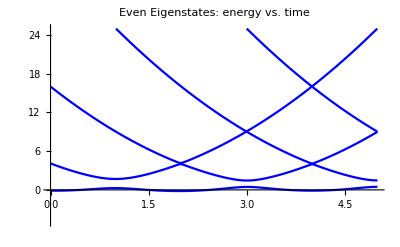

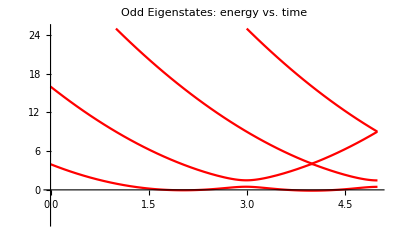

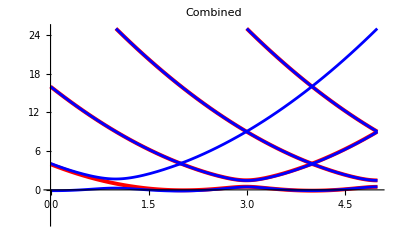

```mathematica
eval = {rr-> 4, Ω -> 1}
Eigs[t_]:=N[Eigensystem[H[t]/.eval]];
EigsSorted[t_] := N@Transpose@SortBy[Transpose[Eigs[t]],First];
EvenEigs[t_] := Table[EigsSorted[t]⟦1⟧⟦i⟧,{i,1,dim,2}];
OddEigs[t_] := Table[EigsSorted[t]⟦1⟧⟦j⟧,{j,2,dim-1,2}];even = Plot[EvenEigs[t], {t, 0, 5}, PlotRange->{{0,5},{-5,25}}, PlotLabel->"Even Eigenstates: energy vs. time", PlotStyle->Blue]
odd = Plot[OddEigs[t], {t, 0, 5}, PlotRange->{{0,5},{-5,25}}, PlotLabel->"Odd Eigenstates: energy vs. time", PlotStyle->Red]
together = Plot[{OddEigs[t],EvenEigs[t]}, {t, 0, 5}, PlotRange->{{0,5},{-5,25}}, PlotLabel->"Combined", PlotStyle->{{Red, Thickness[0.007]},{Blue,Thickness[0.005]}}]
```

Below, I implement integration of the Bloch beamsplitter equations of motion without any assumptions. Then, for calculating projections onto the eigenstates, I use the Hamiltonian matrix after the unitary transformation and rotating wave approximation. You can see that these still describe the final state very well if you ramp slowly and use an appropriate lattice depth.

Hamiltonian matrix for Bloch beamsplitter simulation:

(196 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Cos[0.1 t^2] | 144 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Cos[0.1 t^2] | 100 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[0.1 t^2] | 64 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Cos[0.1 t^2] | 36 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[0.1 t^2] | 16 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 4 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 0 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 4 | Cos[0.1 t^2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 16 | Cos[0.1 t^2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 36 | Cos[0.1 t^2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 64 | Cos[0.1 t^2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 100 | Cos[0.1 t^2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 144 | Cos[0.1 t^2]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[0.1 t^2] | 196)

Hamiltonian with rotating wave approximation (for projection):

((14-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | (12-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | (10-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | (8-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (6-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | (4-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | (2-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0.0025 t^2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (2-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (4-0.05 t)^2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (6-0.05 t)^2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (8-0.05 t)^2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (10-0.05 t)^2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (12-0.05 t)^2 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (14-0.05 t)^2)

Wavefunction after loading lattice:

{3.02229×10^-17,7.02877×10^-14,1.09808×10^-13,2.86651×10^-11,1.20993×10^-7,0.000162207,0.0446236,0.910428,0.0446236,0.000162207,1.20993×10^-7,2.86651×10^-11,1.09808×10^-13,7.02877×10^-14,3.02229×10^-17}

Projection onto first three Bloch bands after loading lattice:

Ground state: 0.98191, First excited state: 0.0180365, Second excited state: 0.0000533644

Wavefunction after Bloch beamsplitter:

{2.23076×10^-9,8.94956×10^-10,4.86704×10^-6,0.00645597,0.47763,0.00558125,0.00124578,0.0181031,0.00124578,0.00558125,0.47763,0.00645597,4.86704×10^-6,8.94956×10^-10,2.23076×10^-9}

Projection onto first three Bloch bands after Bloch beamsplitter:

Ground state: 0.979069, First excited state: 0.000288578, Second excited state: 0.000172831

Wavefunction after unloading lattice:

{1.14463×10^-9,1.13332×10^-11,6.59758×10^-10,0.0000739544,0.489455,0.00021369,0.00154806,0.0173335,0.00154806,0.00021369,0.489455,0.0000739544,6.59758×10^-10,1.13332×10^-11,1.14463×10^-9}

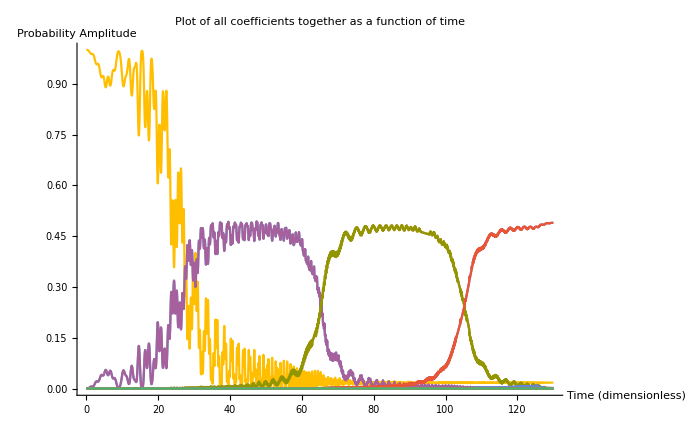

```mathematica
ClearAll["Global`*"];

rGrav = 0.8576; (*This is the dimensionless ramp rate for 852nm light that corresponds to gravitational acceleration 9.8 m/s^2. This value is 23 kHz/ms converted with a factor of 2 π x (2.066 kHz)^2. We need to convert both 1/s units, but the 23 KHz number is in Hz, not radians/s, so we only need one factor of 2π. *)

(*User defined constants*)

NLatDep = 1;  (*Dimensionless lattice depth, called V' in above text*)
NBloch = 3;    (*Number of Bloch oscillations to simulate*)
r = 0.2;  (*r is the dimensionless ramp rate. For gravity, set r = rGrav*)
v0 = 0;    (*Dimensionless initial velocity. ***FOR NOW, THIS CODE IS ONLY GAURANTEED TO WORK FOR v0 ∈ [-1,1)*** *)
tLoad = 5;  (*Length of time used to adiabatically load state into the lattice *)
debug = 1;   (* Set to 1 for extra imformation throughout the simulation, or 0 if you get irritated with all the info *)

(*Implicitly defined constants*)

k0 = Mod[v0+1,2]-1 ;  (*Initial quasimomentum, defined in the range [-1,1) *)
n0 = 0;                     (* Initial momentum state based on v0. ***Should be 0 for this simulation!!*** *)
Δw = 8 n0;                            (* This is the initial frequency required -- not needed? *)
κ = NLatDep/8;
BlochPeriod = 8/r;
TBloch = BlochPeriod * NBloch;
kMax = Max[6,NBloch + 4 + n0];  (*This ensures that in the worst case scenario, amplitude never hits the momentum boundaries of the simulation. VERY deep lattice depths will require extra momentum states as padding since these states may actually get populated*)
dim = kMax*2+1;

(*This loadLattice module creates the initial state and loads it into the lattice. It takes in an initial free space momentum state n0 for a wavefunction, size of the hamiltonian being simulated, time to load lattice, and a load hamiltonian which is a function of time. It solves the Schrodinger equation for 
the wave function while loading the atom into the lattice  and returns this wave function. *)

loadLattice[kMax_, nn0_, tLoad_, loadHam_]:= Module[{maxK= kMax, n0 = nn0, loadTime = tLoad, HamLoad = loadHam},
Clear[ψ, ψi, ψci, ics, cs];

dimState = 2*maxK + 1;
ψi = ConstantArray[0,dimState];
ψi⟦n0 + maxK+1⟧ = 1;

ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];
ics = Table[ ci[n][0]==ψi⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ HamLoad[t].ψ[t];
sol = NDSolve[{equation,ics},cs,{t,0,loadTime}];
ψcii[t_]=ψ[t]/.sol⟦1⟧;
ψcii  (*Returns full wavefunction*)
]

(*unloadLattice is a module that takes in the size of the hamiltonian being simulated, the time taken to unload the atoms (assumed to be the same as the load time), the unload hamiltonian as a function of time, and the state to be unloaded. It returns the state evolution during unload, so ψci[tLoad] is the final free space wavefunction. *)

unLoadLattice[kMax_, tLoad_, unLoadHam_, ψci_]:= Module[{maxK= kMax, loadTime = tLoad, HamUnLoad = unLoadHam, ψi= ψci},
Clear[ψ, ics, cs];

ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];
ics = Table[ ci[n][0]==ψi⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ HamUnLoad[t].ψ[t];
sol = NDSolve[{equation,ics},cs,{t,0,tLoad}];
ψcff[t_]=ψ[t]/.sol⟦1⟧;
ψcff
]


(*Define Hamiltonian matrices. The base hamiltonian is Ham0. I then specialize this to the load and unload hamiltonians, and the main hamiltonian for BO is Ham1. Use sparse array for faster matrix operations. *)

Ham0 = Normal@SparseArray[{{m_,m_}:>(2(m - (kMax+1)))^2,{a_,b_}:> Ω(Exp[- ⅈ Δw t] Cos[rr/2+Δwm t+ϕ]) /; a-b==1,{c_,d_}:> Ω (Exp[ⅈ Δw t] Cos[rr/2+Δwm t+ϕ])/;d-c==1},{dim,dim}];
HamLoad[t_] = Ham0/.{ Ω->NLatDep t/tLoad, rr->0, Δw -> k0, Δwm->0, ϕ->  0 };
HamUnLoad[t_]=Ham0/.{Ω->NLatDep (tLoad-t)/tLoad, rr-> 0 , Δw -> k0, Δwm->r TBloch, ϕ-> r TBloch^2/2};
Ham1[t_]=Ham0/.{Ω->NLatDep , rr->r t^2, Δw -> k0, Δwm->0, ϕ->0};



(*Set up Hamiltonian and unitary operator for projection. This Hamiltonian matrix is what you get if you use the unitary below and then make a rotating wave approximation. *)

HamRWA[t_] = Normal[SparseArray[{{m_,m_}:>(2Abs[m - (kMax+1)] - (r t)/4)^2,{a_,b_}:> NLatDep/2(Exp[- ⅈ k0 t]) /; a-b==1,{m_,n_}:> NLatDep/2(Exp[ ⅈ k0 t])/;n-m==1},{dim,dim}]];
Unitary[t_] = Normal[SparseArray[{{m_,m_}:>Exp[ⅈ (r t^2)/2 Abs[m - (kMax+1)]- ⅈ((r^2 t^3)/(3 16))]},{dim,dim}]];



(*Returns the main BBS Hamiltonian in matrix form *)
If[debug == 1,Print["Hamiltonian matrix for Bloch beamsplitter simulation: "];Print[MatrixForm[Ham1[t]]]; 
Print["Hamiltonian with rotating wave approximation (for projection): "];Print[MatrixForm[HamRWA[t]]]]


(*Begin integration*)

(*load lattice using module*)
ψiBloch =  loadLattice[kMax, n0, tLoad, HamLoad];

(*Return the amplitude squared after loading *)
If[debug ==1, Print["Wavefunction after loading lattice: "];Abs[ψiBloch[tLoad]]^2]

(*See projection of loaded wave function onto the first three Bloch bands. If loaded adiabatically, should be entirely in ground state. *)
If[debug == 1, Print["Projection onto first three Bloch bands after loading lattice:"];
{eValsLoad,eVecsLoad}=Eigensystem[HamRWA[0]];{eValsLoadSorted,eVecsLoadSorted} = Transpose[SortBy[Transpose[{eValsLoad,eVecsLoad}],First]];
i1 =  Norm[ψiBloch[tLoad].eVecsLoadSorted⟦1⟧]^2;
i2 =  Norm[ψiBloch[tLoad].eVecsLoadSorted⟦3⟧]^2;
i3 =  Norm[ψiBloch[tLoad].eVecsLoadSorted⟦5⟧]^2;
Print["Ground state: ",i1,", First excited state: ", i2, ", Second excited state: ", i3];Print[" "];Print[" "]]

(*Now, set up NDSolve to solve the Schrodinger equation for Bloch beamsplitter *)
ψ[t_]=Table[ ci[n][t],{n,-kMax,kMax,1}];
cs = Table[ ci[n],{n,-kMax,kMax,1}];

(* Solve the main Schrodinger equation for BBS *)
ics = Table[ ci[n][0]==ψiBloch[tLoad]⟦n+(kMax+1)⟧,{n,-kMax,kMax,1}];
equation = ψ'[t]== -ⅈ Ham1[t].ψ[t];
soln = NDSolve[{equation,ics},cs,{t,0,TBloch}];
ψci[t_]=ψ[t]/.soln⟦1⟧;

(*Return the amplitude squared after bloch oscillations *)
If[debug == 1, Print["Wavefunction after Bloch beamsplitter: "];Abs[ψci[TBloch]]^2]

(*Look at projection onto different bloch bands after BOs are done *)
If[debug == 1, Print["Projection onto first three Bloch bands after Bloch beamsplitter: "];
{eValsFinal,eVecsFinal}=Eigensystem[HamRWA[TBloch]];{eValsFinalSorted,eVecsFinalSorted} = Transpose[SortBy[Transpose[{eValsFinal,eVecsFinal}],First]];
p1 =  Abs[eVecsFinalSorted⟦1⟧.Unitary[TBloch].ψci[TBloch]]^2;
p2 =  Abs[eVecsFinalSorted⟦3⟧.Unitary[TBloch].ψci[TBloch]]^2;
p3 =  Abs[eVecsFinalSorted⟦5⟧.Unitary[TBloch].ψci[TBloch]]^2;
Print["Ground state: ",p1,", First excited state: " ,p2, ", Second excited state: ",p3];Print[" "];Print[" "]]

(*Unload lattice *)
ψfBloch = unLoadLattice[kMax, tLoad, HamUnLoad, ψci[TBloch]];

(*Return magnitude squared of final free space wave function *)
If[debug ==1, Print["Wavefunction after unloading lattice: "];Abs[ψfBloch[tLoad]]^2]

(*Plot time domain BO solution during main Hamiltonian *)
load = Plot[Evaluate[Hold[(Abs[ψiBloch[t]]^2)⟦#⟧]&/@Range@dim], {t,0,tLoad}, PlotRange->All];
BO = Plot[Evaluate[Hold[(Abs[ψci[t-tLoad]]^2)⟦#⟧]&/@Range@dim], {t,tLoad,tLoad + TBloch}, PlotRange->All];
unload = Plot[Evaluate[Hold[(Abs[ψfBloch[t-tLoad - TBloch]]^2)⟦#⟧]&/@Range@dim], {t,tLoad + TBloch,2 tLoad + TBloch}, PlotRange->All];
Show[{load, BO, unload}, AxesLabel-> {"Time (dimensionless)", "Probability Amplitude"}, ImageSize-> {700,400}, PlotLabel-> "Plot of all coefficients together as a function of time" ]
```